```mathematica
θ[x_]:=If[x>0, x, 0]
k:=0.000086
α[E_,Eg_,T_,AC_,Ep_]:=AC*(θ[E-Eg+Ep]^2/(ⅇ^(Ep/(k*T))-1)+θ[E-Eg-Ep]^2/(1-ⅇ^(-Ep/(k*T))))
```

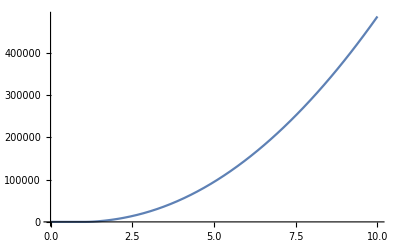

```mathematica
Plot[α[x, 1.12, 300, 6199, 0.061], {x, 0, 10}]
```

```mathematica
trans[E_,Eg_,T_,AC_,Ep_, l_]:=  ⅇ^(-α[E,Eg,T,AC,Ep]*l)
abs[E_,Eg_,T_,AC_,Ep_, l_]:=1-trans[E,Eg,T,AC,Ep, l]
```

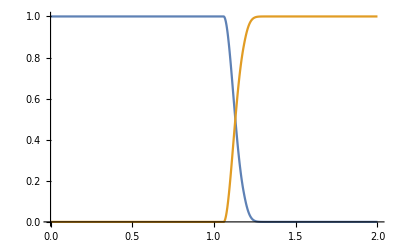

```mathematica
Plot[{trans[x, 1.12, 300, 6199, 0.061, 0.06], abs[x, 1.12, 300, 6199, 0.061, 0.06]}, {x, 0, 2}]
```

```mathematica
abs1[E_,Eg_,T_,AC_,Ep_, l_, A0_]:=A0*(1-trans[E,Eg,T,AC,Ep, l])*ⅇ^(-α[E,Eg,T,AC,Ep]*l)
```

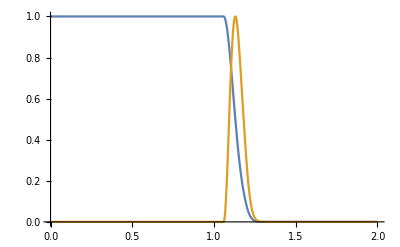

```mathematica
Plot[{trans[x, 1.12, 300, 6199, 0.061, 0.06], abs1[x, 1.12, 300, 6199, 0.061, 0.06, 4]}, {x, 0, 2}]
```